# KASUS TOV SCgrav Ho-Matsuo (juga pakai constant energy density)

## Pers gerak

```mathematica
pers100:=-1/(8 r[rs]^2)(2(α ν''[rs]-2 r[rs] ν'[rs] r'[rs])+4 r[rs] r''[rs]+2κ r[rs]^2 p0 Exp[ν[rs]/2]-α ν'[rs]^2)
pers200:=1/(4 r[rs]^2)(-α ν''[rs]-2(r[rs] r''[rs]+r'[rs]^2)+Exp[ν[rs]](2-κ r[rs]^2(2ρ0-p0 Exp[-ν[rs]/2])))
```

```mathematica
8 r[rs]^2(pers100-pers200)//Simplify
```

-4 ⅇ^ν[rs]+(-4 ⅇ^(ν[rs]/2) p0 κ+4 ⅇ^ν[rs] κ ρ0) r[rs]^2+4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2

```mathematica
8 r[rs]^2(pers100+pers200)//Simplify
```

4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-2 r''[rs])-4 α ν''[rs]

```mathematica
ClearAll["Global`*"]
persν:=-4 ⅇ^ν[rs]+(-4 ⅇ^(ν[rs]/2) p0 κ+4 ⅇ^ν[rs] κ ρ0) r[rs]^2+4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2
persr:=4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-2 r''[rs])-4 α ν''[rs]
(*ρ0[rs_]=Piecewise[{{0./κ,rs>y},{25./κ,rs≤y}}]/.{y->-60.};*)

Solve[persν==0,ν'[rs]]//FullSimplify
limitαnol-> Solve[(persν/.{α->0})==0,ν'[rs]]//FullSimplify

Solve[persr==0,r''[rs]]//Simplify
```

{{ν'[rs]→-(2 (r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))))/α},{ν'[rs]→(2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))))/α}}

limitαnol→{{ν'[rs]→(ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(r[rs] r'[rs])}}

{{r''[rs]→(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2-4 α ν''[rs])/(8 r[rs])}}

```mathematica
rootpertama-> Series[-1/α 2 (r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))),{α,0,1}]//Simplify
rootkedua-> Series[1/α 2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))),{α,0,1}]//Simplify
```

rootpertama→-(2 (r[rs] r'[rs]+√(r[rs]^2 r'[rs]^2)))/α+(-ⅇ^ν[rs]+(-ⅇ^(ν[rs]/2) p0 κ+ⅇ^ν[rs] κ ρ0) r[rs]^2+r'[rs]^2)/(√(r[rs]^2 r'[rs]^2))+(√(r[rs]^2 r'[rs]^2) (-ⅇ^ν[rs]+(-ⅇ^(ν[rs]/2) p0 κ+ⅇ^ν[rs] κ ρ0) r[rs]^2+r'[rs]^2)^2 α)/(4 r[rs]^4 r'[rs]^4)+O[α]^2

rootkedua→(2 (-r[rs] r'[rs]+√(r[rs]^2 r'[rs]^2)))/α+(ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(√(r[rs]^2 r'[rs]^2))-((√(r[rs]^2 r'[rs]^2) (-ⅇ^ν[rs]+(-ⅇ^(ν[rs]/2) p0 κ+ⅇ^ν[rs] κ ρ0) r[rs]^2+r'[rs]^2)^2) α)/(4 (r[rs]^4 r'[rs]^4))+O[α]^2

rootkedua kembali ke TOV

### Jadi pers geraknya yg bisa ditulis eksplisit adalah

```mathematica
pers1:=ν'[rs]-> 1/α 2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))
(*Persamaan differensial metrik*)
pers2:=r''[rs]-> 1/(8 r[rs])(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ r[rs]^2 ρ0-4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2-4 α ν''[rs])(*Persamaan differensial radius*)
```

```mathematica
pers2/.{pers1,D[pers1,rs]}//Simplify
```

r''[rs]→1/(8 r[rs])(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+(8 r[rs] r'[rs] (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))))/α+(4 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))^2)/α-8 (-r'[rs]^2-r[rs] r''[rs]+(4 r[rs] r'[rs] (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)+2 α (ⅇ^ν[rs] ν'[rs]-2 r'[rs] r''[rs])+r[rs]^2 ((ⅇ^(ν[rs]/2) p0 α κ-2 ⅇ^ν[rs] α κ ρ0) ν'[rs]+4 r'[rs] r''[rs]))/(4 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))))

### Membandingkan dengan persaman TOV GR

```mathematica
ClearAll["Global`*"]
persν:=-4 ⅇ^ν[rs]+(-4 ⅇ^(ν[rs]/2) p0 κ+4 ⅇ^ν[rs] κ ρ0) r[rs]^2+4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+0α ν'[rs]^2
persr:=4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+0α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-2 r''[rs])-4 0 α ν''[rs]
(*ρ0[rs_]=Piecewise[{{0./κ,rs>y},{25./κ,rs≤y}}]/.{y->-60.};*)

Solve[persν==0,ν'[rs]]//FullSimplify

Solve[persr==0,r''[rs]]//Simplify
```

{{ν'[rs]→(ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(r[rs] r'[rs])}}

{{r''[rs]→(ⅇ^ν[rs]-ⅇ^ν[rs] κ ρ0 r[rs]^2-r'[rs]^2+r[rs] r'[rs] ν'[rs])/(2 r[rs])}}

```mathematica
pers3:=ν'[rs]-> (ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(r[rs] r'[rs])
(*Persamaan differensial metrik*)
pers4:=r''[rs]->(ⅇ^ν[rs]-ⅇ^ν[rs] κ ρ0 r[rs]^2-r'[rs]^2+r[rs] r'[rs] ν'[rs])/(2 r[rs])
(*Persamaan differensial radius*)
pers4/.{pers3}//Simplify
```

r''[rs]→((ⅇ^(ν[rs]/2) p0 κ-2 ⅇ^ν[rs] κ ρ0) r[rs]^2+2 (ⅇ^ν[rs]-r'[rs]^2))/(2 r[rs])

### Backward calculation Ho-Matsuo

```mathematica
Clear["Global`*"]
pers1=-ν'[rs]+1/α 2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)));
(*Persamaan differensial metrik*)
pers2=-r''[rs]+1/(8 r[rs])(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+1/α 8 r[rs] r'[rs] (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))+1/α 4 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))^2-8 (-r'[rs]^2-r[rs] r''[rs]+(4 r[rs] r'[rs] (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)+2 α (ⅇ^ν[rs] ν'[rs]-2 r'[rs] r''[rs])+r[rs]^2 ((ⅇ^(ν[rs]/2) p0 α κ-2 ⅇ^ν[rs] α κ ρ0) ν'[rs]+4 r'[rs] r''[rs]))/(4 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))));(*Persamaan differensial radius*)
```

```mathematica
GS=1.325*10^-12; MSS= 1.1155 * 10^15;
```

10.

-266.309

{{ν→InterpolatingFunction[{{-600000., -266.309}}, <>],r→InterpolatingFunction[{{-600000., -266.309}}, <>]}}

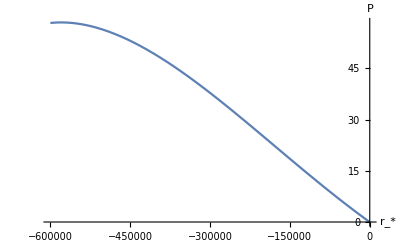

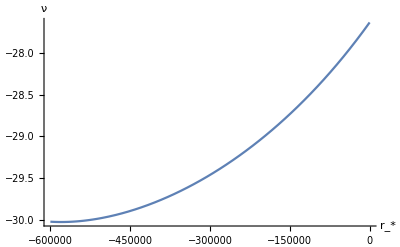

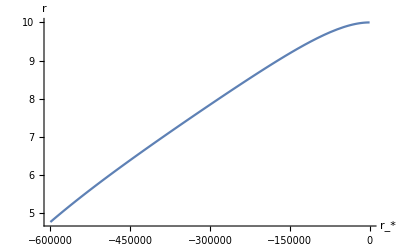

```mathematica
α=0.05;
κ =8π GS;
a0:=10.
ρ00:=25.2
R=10./0.999999999999
rn=-600000;
rs0=R+a0 Log[R/a0-1]
ν0=Log[1-a0/R];
ρ0=ρ00/κ;
p0=ρ00/κ Exp[ν0/2.];
s=NDSolve[{pers1==0,pers2==0,ν[rs0]==ν0,r[rs0]==R,r'[rs0]==(1-a0/R)},{ν,r},{rs,rs0,rn}]
νo[rs_]=Evaluate[ν[rs]/.s][[1]];
ro[rs_]=Evaluate[r[rs]/.s][[1]];
Po[rs_]:=-ρ0 +p0 Exp[-νo[rs]/2]

xx=rn;
Plot[κ Po[rs],{rs,xx,rs0},AxesLabel->{"r_*","P"},PlotRange->All]
Plot[νo[rs],{rs,xx,rs0},AxesLabel->{"r_*","ν"},PlotRange->All]
Plot[ro[rs],{rs,xx,rs0},AxesLabel->{"r_*","r"},PlotRange->All]
```

### Forward

{{ν→InterpolatingFunction[{{-600000., -266.309}}, <>],r→InterpolatingFunction[{{-600000., -266.309}}, <>]}}

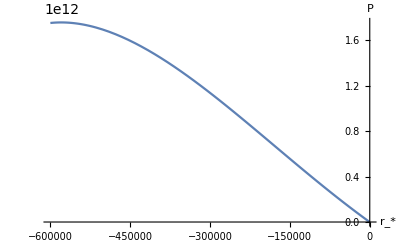

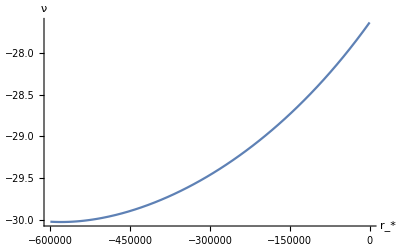

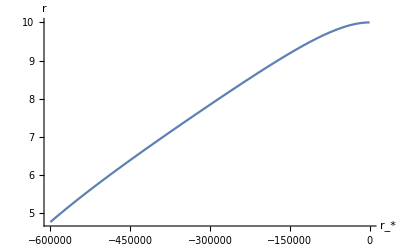

```mathematica
s1=NDSolve[{pers1==0,pers2==0,ν[rn]==νo[rn],r[rn]==ro[rn],r'[rn]==ro'[rn]},{ν,r},{rs,rn,rs0}]
νo1[rs_]=Evaluate[ν[rs]/.s1][[1]];
ro1[rs_]=Evaluate[r[rs]/.s1][[1]];
Po1[rs_]:=-ρ0 +p0 Exp[-νo1[rs]/2]

xx=rn;
Plot[Po1[rs],{rs,xx,rs0},AxesLabel->{"r_*","P"},PlotRange->All]
Plot[νo1[rs],{rs,xx,rs0},AxesLabel->{"r_*","ν"},PlotRange->All]
Plot[ro1[rs],{rs,xx,rs0},AxesLabel->{"r_*","r"},PlotRange->All]
```

### Perbandingan Backward vs Forward

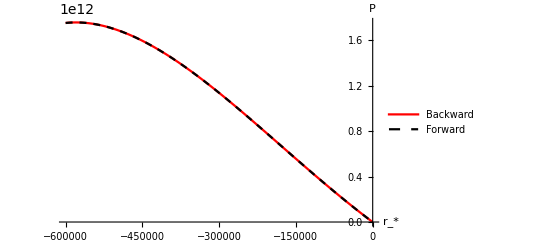

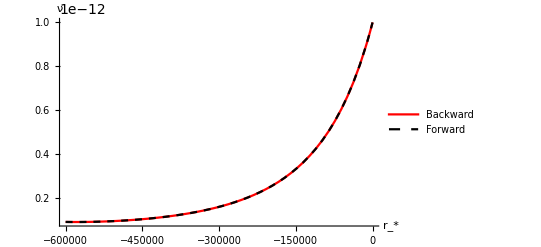

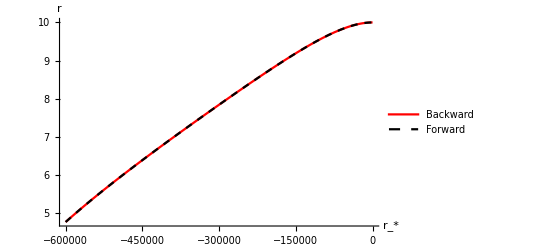

```mathematica
Plot[{ Po1[rs], Po[rs]},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_*","P"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward","Forward"}]
Plot[{Exp[νo1[rs]],Exp[νo[rs]]},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_*","ν"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward","Forward"}]
Plot[{ro1[rs],ro[rs]},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_*","r"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward","Forward"}]
```

### Forward calculation TOV GR

```mathematica
pers3=-ν'[rs]+(ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(r[rs] r'[rs]);
(*Persamaan differensial metrik*)
pers4=-r''[rs]+((ⅇ^(ν[rs]/2) p0 κ-2 ⅇ^ν[rs] κ ρ0) r[rs]^2+2 (ⅇ^ν[rs]-r'[rs]^2))/(2 r[rs]);(*Persamaan differensial radius*)
```

```mathematica
{ν[rn]==νo[rn],r[rn]==ro[rn],r'[rn]==ro'[rn]}
```

{ν[-600000]==-30.0262,r[-600000]==4.77393,r'[-600000]==0.0000119695}

{{ν→InterpolatingFunction[{{-600000., -266.309}}, <>],r→InterpolatingFunction[{{-600000., -266.309}}, <>]}}

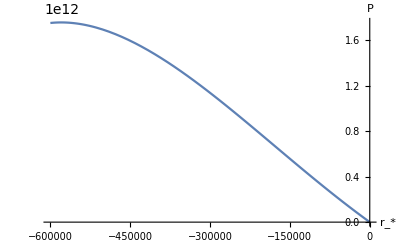

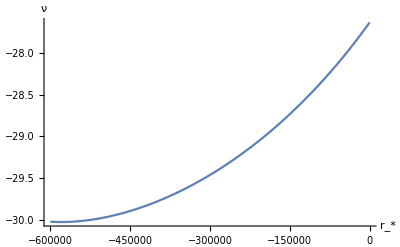

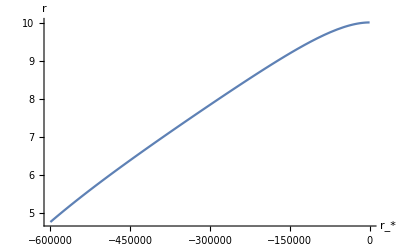

```mathematica
s3=NDSolve[{pers3==0,pers4==0,ν[rn]==νo[rn],r[rn]==ro[rn],r'[rn]==ro'[rn]},{ν,r},{rs,rn,rs0}]
νo1tov[rs_]=Evaluate[ν[rs]/.s3][[1]];
ro1tov[rs_]=Evaluate[r[rs]/.s3][[1]];
Po1tov[rs_]:=-ρ0 +p0 Exp[-νo1tov[rs]/2]

xx=rn;
Plot[Po1tov[rs],{rs,xx,rs0},AxesLabel->{"r_*","P"},PlotRange->All]
Plot[νo1tov[rs],{rs,xx,rs0},AxesLabel->{"r_*","ν"},PlotRange->All]
Plot[ro1tov[rs],{rs,xx,rs0},AxesLabel->{"r_*","r"},PlotRange->All]
```

### Backward TOV GR

```mathematica
{ν[rs0]==ν0,r[rs0]==R,r'[rs0]==(1-a0/R)}
{ν[rs0]==νo1tov[rs0],r[rs0]==ro1tov[rs0],r'[rs0]==ro1tov'[rs0]}
```

{ν[-266.309]==-27.6309,r[-266.309]==10.,r'[-266.309]==1.00009×10^-12}

{ν[-266.309]==-27.6337,r[-266.309]==10.0089,r'[-266.309]==4.9972×10^-8}

{{ν→InterpolatingFunction[{{-600000., -266.309}}, <>],r→InterpolatingFunction[{{-600000., -266.309}}, <>]}}

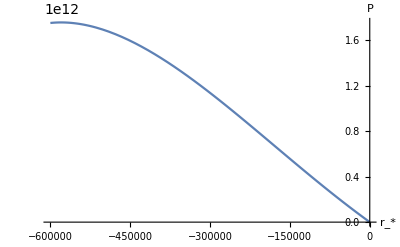

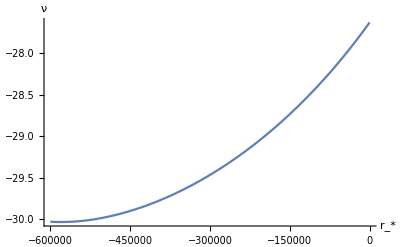

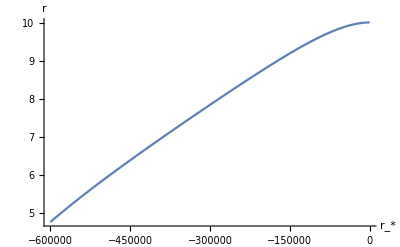

```mathematica
s3=NDSolve[{pers3==0,pers4==0,ν[rs0]==νo1tov[rs0],r[rs0]==ro1tov[rs0],r'[rs0]==ro1tov'[rs0]},{ν,r},{rs,rs0,rn}]
νotov[rs_]=Evaluate[ν[rs]/.s3][[1]];
rotov[rs_]=Evaluate[r[rs]/.s3][[1]];
Potov[rs_]:=-ρ0 +p0 Exp[-νotov[rs]/2]

xx=rn;
Plot[ Potov[rs],{rs,xx,rs0},AxesLabel->{"r_*","P"},PlotRange->All]
Plot[νotov[rs],{rs,xx,rs0},AxesLabel->{"r_*","ν"},PlotRange->All]
Plot[rotov[rs],{rs,xx,rs0},AxesLabel->{"r_*","r"},PlotRange->All]
```

### Perbandingan Backward vs Forward

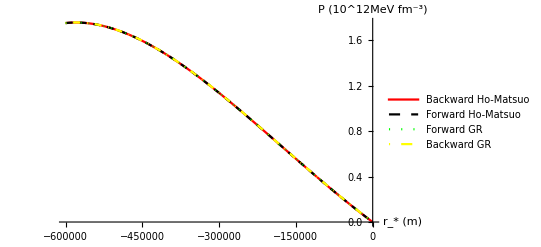

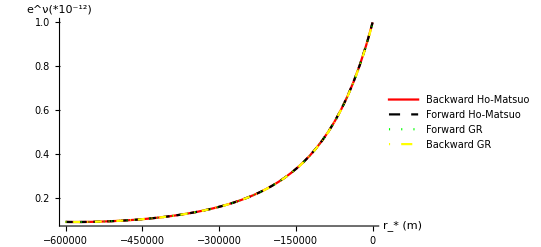

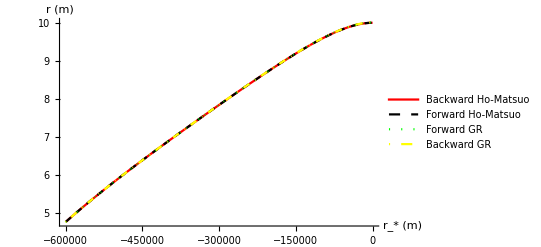

```mathematica
Plot[{Po[rs]*10^-12, Po1[rs]*10^-12,Po1tov[rs]*10^-12, Potov[rs]*10^-12},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_* (m)","P (10^12MeV fm^-3)"},PlotStyle->{{Red,Thick},{Black,Dashed},{Green,Dotted},{Yellow,DotDashed}},PlotLegends->{"Backward Ho-Matsuo","Forward Ho-Matsuo","Forward GR","Backward GR"}]
Plot[{Exp[νo[rs]]*10^12,Exp[νo1[rs]]*10^12,Exp[νo1tov[rs]]*10^12,Exp[νotov[rs]]*10^12},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_* (m)","e^ν(*10^-12)"},PlotStyle->{{Red,Thick},{Black,Dashed},{Green,Dotted},{Yellow,DotDashed}},PlotLegends->{"Backward Ho-Matsuo","Forward Ho-Matsuo","Forward GR","Backward GR"}]
Plot[{ro[rs],ro1[rs],ro1tov[rs],rotov[rs]},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_* (m)","r (m)"},PlotStyle->{{Red,Thick},{Black,Dashed},{Green,Dotted},{Yellow,DotDashed}},PlotLegends->{"Backward Ho-Matsuo","Forward Ho-Matsuo","Forward GR","Backward GR"}]
```

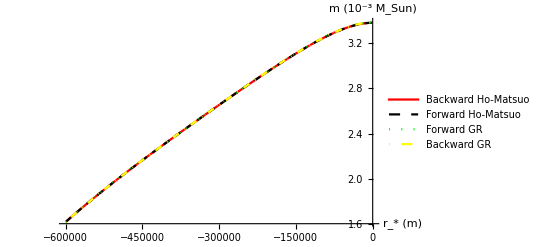

```mathematica
mo[rs_]:=ro[rs]/(2GS MSS)(1-ro'[rs])
mo1[rs_]:=ro1[rs]/(2GS MSS)(1-ro1'[rs])
mo1tov[rs_]:=ro1tov[rs]/(2GS MSS)(1-ro1tov'[rs])
motov[rs_]:=rotov[rs]/(2GS MSS)(1-rotov'[rs])
Plot[{mo[rs]*10^3,mo1[rs]*10^3,mo1tov[rs]*10^3,motov[rs]*10^3},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_* (m)","m (10^-3 M_Sun)"},PlotStyle->{{Red,Thick},{Black,Dashed},{Green,Dotted},{Yellow,DotDashed}},PlotLegends->{"Backward Ho-Matsuo","Forward Ho-Matsuo","Forward GR","Backward GR"}]
```

Keluarin datanya

```mathematica
R-a0
```

1.00009×10^-11

```mathematica
ClearAll[x]
x[i_]:=rn+i(rs0-rn)/1000
data:=Table[{x[i]/100000,Po[x[i]]*10^-12, Po1[x[i]]*10^-12,Po1tov[x[i]]*10^-12, Potov[x[i]]*10^-12,mo[x[i]], mo1[x[i]],mo1tov[x[i]], motov[x[i]],Exp[νo[x[i]]]*10^12,Exp[νo1[x[i]]]*10^12,Exp[νo1tov[x[i]]]*10^12, Exp[νotov[x[i]]]*10^12,ro[x[i]], ro1[x[i]],ro1tov[x[i]], rotov[x[i]]},{i,0,1000}]
Export[FileNameJoin[{NotebookDirectory[],"TOV-reverse-5.0.dat"}],data]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\TOV-reverse-5.0.dat